```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/enrico/Dropbox/Git_repo/website/EnricoMalatesta/blog/2025

```mathematica
smicro[J_,e_]:=Piecewise[{{Log[2]-(J e^2)/2,-√(2J Log[2])<=e<=√(2J Log[2])},{0,e>√(2J Log[2])},{0,e<√(2J Log[2])}}];
smicroder[J_,e_]:=-J e;
```

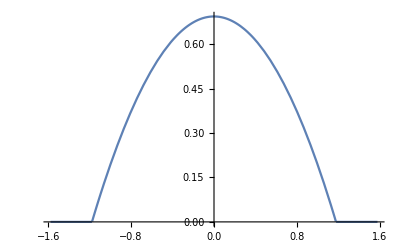

```mathematica
With[{J=1},Plot[smicro[J,e],{e,-√(2J Log[2])-0.4,√(2J Log[2])+0.4}]]
```

```mathematica
With[{J=1},Manipulate[Plot[smicro[J,e]-β e,{e,-√(2J Log[2])-0.2,√(2J Log[2])-0.2}],{β,0,10}]]
```

```mathematica
tangent[J_,es_,e_]:=smicro[J,es]+smicroder[J,es] (e-es);
```

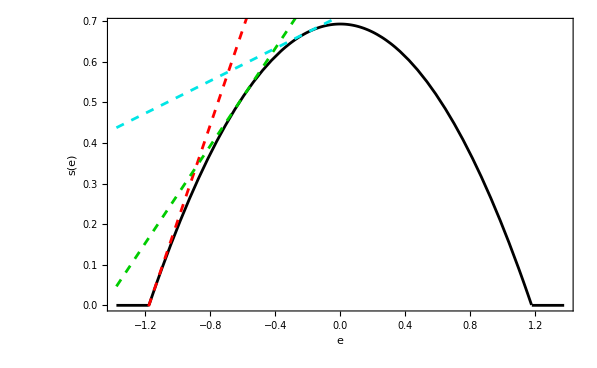

```mathematica
plot=With[{J=1,β=√(2Log[2]),βp=0.6,βpp=0.2},Show[Plot[smicro[J,e],{e,-√(2J Log[2])-0.2,√(2J Log[2])+0.2},PlotStyle->{Black,AbsoluteThickness[2]},Frame->{True},FrameLabel->{Style["e",16,Bold,Black],(*bottom*)Style["s(e)",16,Bold,Black]     (*left*)}
],Plot[{tangent[J,-β/J,e],tangent[J,-βp/J,e],tangent[J,-βpp/J,e]},{e,-√(2J Log[2])-0.2,0.2},PlotStyle->{{Red,Dashing[{0.01,0.01}],AbsoluteThickness[2]},{Darker[Green,0.2],Dashing[{0.01,0.01}],AbsoluteThickness[2]},{Darker[Cyan,0.1],Dashing[{0.01,0.01}],AbsoluteThickness[2]}}]]]
```

```mathematica
Export["rem_entropy.png",plot,ImageSize->{600,400}]
```

rem_entropy.png



```mathematica
plot=Plot[Sin[x],{x,0,2 Pi}]
```